```mathematica
T1=(1/2)*M1*L1^2/3*v1^2
```

1/6 L1^2 M1 v1^2

```mathematica
T2=1/2*M2*(L2^2/3*(v1+v2)^2+L1^2v1^2+L1*L2*v1*(v1+v2)*Cos[t])
```

1/2 M2 (L1^2 v1^2+1/3 L2^2 (v1+v2)^2+L1 L2 v1 (v1+v2) Cos[t])

```mathematica
TT=T1+T2
```

1/6 L1^2 M1 v1^2+1/2 M2 (L1^2 v1^2+1/3 L2^2 (v1+v2)^2+L1 L2 v1 (v1+v2) Cos[t])

```mathematica
a11=D[TT, q1]
a12=D[TT, v1]
a12t=D[a12, q1]*v1+D[a12, q2]*v2+D[a12, v1]*a1+D[a12,v2]*a2
```

0

1/3 L1^2 M1 v1+1/2 M2 (2 L1^2 v1+2/3 L2^2 (v1+v2)+L1 L2 v1 Cos[t]+L1 L2 (v1+v2) Cos[t])

1/2 a2 M2 ((2 L2^2)/3+L1 L2 Cos[t])+a1 ((L1^2 M1)/3+1/2 M2 (2 L1^2+(2 L2^2)/3+2 L1 L2 Cos[t]))

```mathematica
a21=D[TT, q2]
a22=D[TT,v2]
a22t=D[a12, q1]*v1+D[a22, q2]*v2+D[a22, v1]*a1+D[a22,v2]*a2
```

0

1/2 M2 (2/3 L2^2 (v1+v2)+L1 L2 v1 Cos[t])

1/3 a2 L2^2 M2+1/2 a1 M2 ((2 L2^2)/3+L1 L2 Cos[t])

```mathematica
eq1=a12t-a11==u1
eq2=a22t-a21==u2
```

1/2 a2 M2 ((2 L2^2)/3+L1 L2 Cos[t])+a1 ((L1^2 M1)/3+1/2 M2 (2 L1^2+(2 L2^2)/3+2 L1 L2 Cos[t]))==u1

1/3 a2 L2^2 M2+1/2 a1 M2 ((2 L2^2)/3+L1 L2 Cos[t])==u2

```mathematica
s1=Solve[{eq1,eq2}, {a1,a2}]
```

{{a1→-(6 (-2 L2 u1+2 L2 u2+3 L1 u2 Cos[t]))/(L1^2 L2 (4 M1+12 M2-9 M2 Cos[t]^2)),a2→-(6 (-2 L2^2 M2 u1+2 L1^2 M1 u2+6 L1^2 M2 u2+2 L2^2 M2 u2-3 L1 L2 M2 u1 Cos[t]+6 L1 L2 M2 u2 Cos[t]))/(L1^2 L2^2 M2 (-4 M1-12 M2+9 M2 Cos[t]^2))}}

```mathematica
EQ={a1,a2}/.s1
```

{{-(6 (-2 L2 u1+2 L2 u2+3 L1 u2 Cos[t]))/(L1^2 L2 (4 M1+12 M2-9 M2 Cos[t]^2)),-(6 (-2 L2^2 M2 u1+2 L1^2 M1 u2+6 L1^2 M2 u2+2 L2^2 M2 u2-3 L1 L2 M2 u1 Cos[t]+6 L1 L2 M2 u2 Cos[t]))/(L1^2 L2^2 M2 (-4 M1-12 M2+9 M2 Cos[t]^2))}}

```mathematica
EQQ=Flatten[EQ/.{q1->q1[t], q2->q2[t],v1->q1'[t],v2->q2'[t],L1->1,L2->1,M1->1,M2->1,u1->u1[t],u2->u2[t]}]
```

{-(6 (-2 u1[t]+2 u2[t]+3 Cos[t] u2[t]))/(16-9 Cos[t]^2),-(6 (-2 u1[t]-3 Cos[t] u1[t]+10 u2[t]+6 Cos[t] u2[t]))/(-16+9 Cos[t]^2)}

```mathematica
EQQQ={q1''[t]==EQQ[[1]],q2''[t]==EQQ[[2]]}
```

{q1''[t]==-(6 (-2 u1[t]+2 u2[t]+3 Cos[t] u2[t]))/(16-9 Cos[t]^2),q2''[t]==-(6 (-2 u1[t]-3 Cos[t] u1[t]+10 u2[t]+6 Cos[t] u2[t]))/(-16+9 Cos[t]^2)}

```mathematica
tf=10
kp=5^2
kd=2*5
sol=NDSolve[{EQQQ[[1]], EQQQ[[2]], q1[0]==0, q2[0]==0, q1'[0]==0, q2'[0]==0, u1[t]==-kd*q1'[t]-kp*(q1[t]-1), u2[t]==-kd*q2'[t]-kd*(q2[t]-(-1/2))}, {q1, q2}, {t, 0, tf}]
```

10

25

10

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

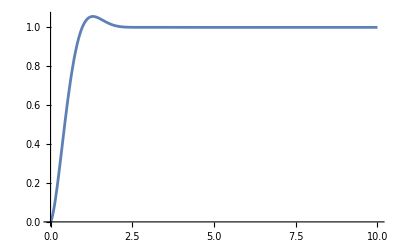

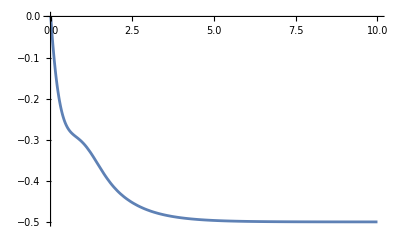

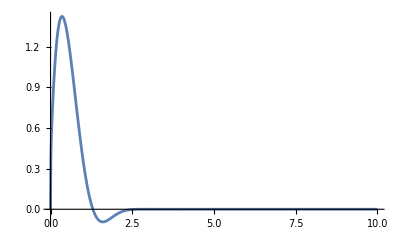

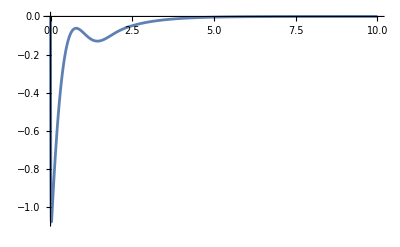

```mathematica
P1=Plot[Evaluate[q1[t]/.sol], {t, 0, tf}, PlotRange->All]
P2=Plot[Evaluate[q2[t]/.sol], {t, 0, tf}, PlotRange->All]
P3=Plot[Evaluate[q1'[t]/.sol], {t, 0, tf}, PlotRange->All]
P4=Plot[Evaluate[q2'[t]/.sol], {t, 0, tf}, PlotRange->All]
```

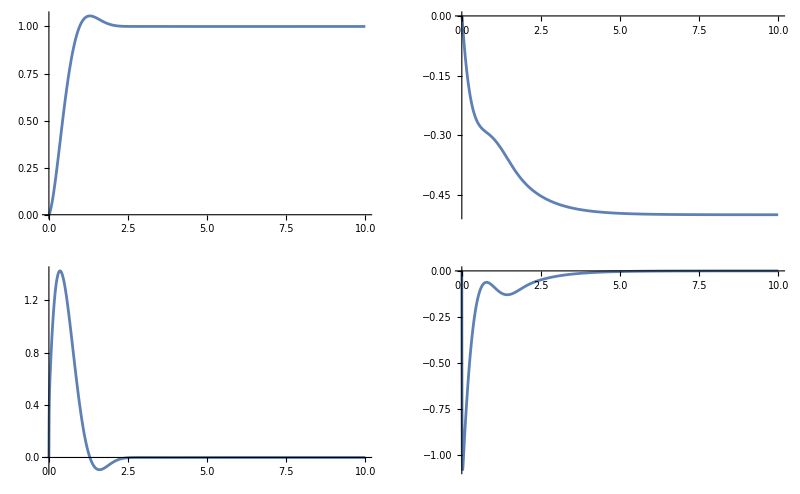

```mathematica
GraphicsGrid[{{P1,P2},{P3,P4}}]
```